```mathematica
SetOptions[EvaluationNotebook[],  CommonDefaultFormatTypes -> {"Output" -> StandardForm}]
```

```mathematica
Integrate[(Γ m)/((x-m^2)^2+(Γ m)^2), {x, a, b}, Assumptions->{m∈Reals, m>0, Γ∈Reals, Γ>0, b>a}]
```

-ArcCot[(m Γ)/(a-m^2)]+ArcCot[(m Γ)/(b-m^2)]

```mathematica
f[t_] := (Re[Q]+ⅈ Im[Q])/(t-m^2+ⅈ Γ m)+(Re[Q]-ⅈ Im[Q])/(t-m^2-ⅈ Γ m)
fint = Integrate[f[t], {t, a, b}, Assumptions->{Q∈Complexes, m∈PositiveReals, m>0, Γ∈PositiveReals, Γ>0, a∈Reals, b∈Reals, b>a, a<m^2, b>m^2}]
```

2 (π+ArcTan[(m Γ)/(a-m^2)]+ArcTan[(m Γ)/(-b+m^2)]) Im[Q]+Log[((b-m^2)^2+m^2 Γ^2)/((a-m^2)^2+m^2 Γ^2)] Re[Q]

Setting  parameters

```mathematica
mi = 100;
mj = 100;
mA = 1000;
GA = 1;
```

Setting up integration boundary functions

```mathematica
p[s_] := Sqrt[(s-(mi-mj)^2)(s-(mi+mj)^2)]
t1[s_] := (mi^2+mj^2-s)/2+Sqrt[s]*p[s]
t0[s_] := (mi^2+mj^2-s)/2-Sqrt[s]*p[s]
```

Actual integral as function of integration boundaries

```mathematica
F[s_] := Integrate[(GA mA)/((x-mA^2)^2 + GA^2mA^2), {x, t0[s], t1[s]}]
Fanalytic = Integrate[(Re[Q]+ⅈ Im[Q])/(t-m^2+ⅈ Γ m)+(Re[Q]-ⅈ Im[Q])/(t-m^2-ⅈ Γ m), {t, a, b}, Assumptions->{Q∈Complexes, m∈PositiveReals, m>0, Γ∈PositiveReals, Γ>0, a∈Reals, b∈Reals, b>a, a<m^2, b>m^2}] //
	ReplaceAll[#, {Re[Q]->0, Im[Q]->1, m->mA, Γ->GA}]&
```

2 (π+ArcTan[10/(-1+a)]+ArcTan[10/(1-b)])

Plotting “analytic” result of integral vs. actual integral value as function of integration boundaries

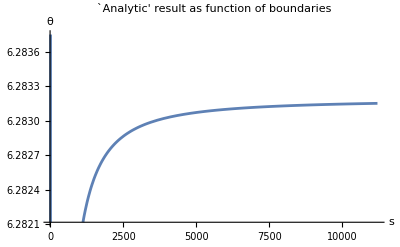

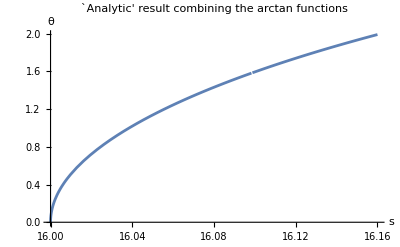

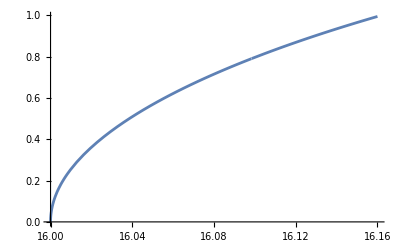

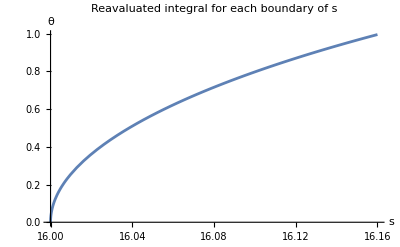

```mathematica
Plot[ReplaceAll[Fanalytic, {a->t0[s], b->t1[s]}], {s, (mi+mj)^2, 1.01(mi+mj)^2}, PlotLabel->"`Analytic' result as function of boundaries", AxesLabel->{"s", "θ"}]
Plot[2 ArcTan[(10/(-1+t0[s])+10/(1-t1[s]))/(1-10/(-1+t0[s])10/(1-t1[s]))],  {s, (mi+mj)^2, 1.01(mi+mj)^2}, PlotLabel->"`Analytic' result combining the arctan functions", AxesLabel->{"s", "θ"}]
Plot[ArcTan[(t1[s]-mA^2)/(GA mA)] - ArcTan[(t0[s]-mA^2)/(GA mA)], {s, (mi+mj)^2, 1.01(mi+mj)^2}]

Plot[F[s], {s, (mi+mj)^2, 1.01(mi+mj)^2}, PlotLabel->"Reavaluated integral for each boundary of s", AxesLabel->{"s", "θ"}]
```

```mathematica
-Graphics-)))-I*(atan2(real(tterm)+Q2p,imag(tterm))-atan2(real(tterm)-Q2p,imag(tterm)));
uLogA=log(abs((uterm+Q2p)/(uterm-Q2p
```

-Graphics-

-Graphics-

```mathematica
Integrate[
	(Re[Q]+ⅈ Im[Q])/((t-m1^2+ⅈ G1 m1)(t-m2^2 - ⅈ G2 m2))+(Re[Q]-ⅈ Im[Q])/((t-m1^2-ⅈ G1 m1)(t-m2^2 + ⅈ G2 m2)),
	{t, a, b},
	Assumptions->{a∈Reals, b∈Reals, b>a, Q∈Complexes, m1∈Reals, G1∈Reals, m1>0, G1>0, m2∈Reals, G2∈Reals, m2>0, G2>0, b>m1^2, b>m2^2, a<m1^2, a<m2^2}
]
% /. {m2->m1, G2->G1}
```

((16 G1 m1 π+16 G1 m1 ArcTan[(G1 m1)/(a-m1^2)]-16 G1 m1 ArcTan[(G1 m1)/(b-m1^2)]+4 ⅈ G1 m1 Log[G1 m1]-2 ⅈ G1 m1 Log[G1^2 m1^2]) Re[Q])/(8 G1^2 m1^2)

(2 Im[Q] (4 m1^2 π-4 m2^2 π+2 (m1^2-m2^2) ArcTan[(G1 m1)/(a-m1^2)]-2 (m1^2-m2^2) ArcTan[(G1 m1)/(b-m1^2)]+2 m1^2 ArcTan[(G2 m2)/(a-m2^2)]-2 m2^2 ArcTan[(G2 m2)/(a-m2^2)]-2 m1^2 ArcTan[(G2 m2)/(b-m2^2)]+2 m2^2 ArcTan[(G2 m2)/(b-m2^2)]+G1 m1 Log[((a^2-2 a m1^2+G1^2 m1^2+m1^4) (b^2-2 b m2^2+G2^2 m2^2+m2^4))/((b^2-2 b m1^2+G1^2 m1^2+m1^4) (a^2-2 a m2^2+G2^2 m2^2+m2^4))]+G2 m2 Log[((a^2-2 a m1^2+G1^2 m1^2+m1^4) (b^2-2 b m2^2+G2^2 m2^2+m2^4))/((b^2-2 b m1^2+G1^2 m1^2+m1^4) (a^2-2 a m2^2+G2^2 m2^2+m2^4))])+(8 G1 m1 π+8 G2 m2 π+4 (G1 m1+G2 m2) ArcTan[(G1 m1)/(a-m1^2)]-4 (G1 m1+G2 m2) ArcTan[(G1 m1)/(b-m1^2)]+4 G1 m1 ArcTan[(G2 m2)/(a-m2^2)]+4 G2 m2 ArcTan[(G2 m2)/(a-m2^2)]-4 G1 m1 ArcTan[(G2 m2)/(b-m2^2)]-4 G2 m2 ArcTan[(G2 m2)/(b-m2^2)]+2 ⅈ G1 m1 Log[G1 m1]-2 m1^2 Log[G1 m1]+2 ⅈ G2 m2 Log[G1 m1]+2 m2^2 Log[G1 m1]-ⅈ G1 m1 Log[G1^2 m1^2]+m1^2 Log[G1^2 m1^2]-ⅈ G2 m2 Log[G1^2 m1^2]-m2^2 Log[G1^2 m1^2]-2 m1^2 Log[a^2-2 a m1^2+G1^2 m1^2+m1^4]+2 m2^2 Log[a^2-2 a m1^2+G1^2 m1^2+m1^4]+2 m1^2 Log[b^2-2 b m1^2+G1^2 m1^2+m1^4]-2 m2^2 Log[b^2-2 b m1^2+G1^2 m1^2+m1^4]+2 m1^2 Log[a^2-2 a m2^2+G2^2 m2^2+m2^4]-2 m2^2 Log[a^2-2 a m2^2+G2^2 m2^2+m2^4]-2 m1^2 Log[b^2-2 b m2^2+G2^2 m2^2+m2^4]+2 m2^2 Log[b^2-2 b m2^2+G2^2 m2^2+m2^4]) Re[Q])/(2 (G1^2 m1^2+m1^4+2 G1 G2 m1 m2+G2^2 m2^2-2 m1^2 m2^2+m2^4))

(2 Im[Q] (4 m1^2 π-4 m2^2 π+2 (m1^2-m2^2) ArcTan[(G1 m1)/(a-m1^2)]-2 (m1^2-m2^2) ArcTan[(G1 m1)/(b-m1^2)]+2 m1^2 ArcTan[(G2 m2)/(a-m2^2)]-2 m2^2 ArcTan[(G2 m2)/(a-m2^2)]-2 m1^2 ArcTan[(G2 m2)/(b-m2^2)]+2 m2^2 ArcTan[(G2 m2)/(b-m2^2)]+G1 m1 Log[((a^2-2 a m1^2+G1^2 m1^2+m1^4) (b^2-2 b m2^2+G2^2 m2^2+m2^4))/((b^2-2 b m1^2+G1^2 m1^2+m1^4) (a^2-2 a m2^2+G2^2 m2^2+m2^4))]+G2 m2 Log[((a^2-2 a m1^2+G1^2 m1^2+m1^4) (b^2-2 b m2^2+G2^2 m2^2+m2^4))/((b^2-2 b m1^2+G1^2 m1^2+m1^4) (a^2-2 a m2^2+G2^2 m2^2+m2^4))])+(8 G1 m1 π+8 G2 m2 π+4 (G1 m1+G2 m2) ArcTan[(G1 m1)/(a-m1^2)]-4 (G1 m1+G2 m2) ArcTan[(G1 m1)/(b-m1^2)]+4 G1 m1 ArcTan[(G2 m2)/(a-m2^2)]+4 G2 m2 ArcTan[(G2 m2)/(a-m2^2)]-4 G1 m1 ArcTan[(G2 m2)/(b-m2^2)]-4 G2 m2 ArcTan[(G2 m2)/(b-m2^2)]+2 ⅈ G1 m1 Log[G1 m1]-2 m1^2 Log[G1 m1]+2 ⅈ G2 m2 Log[G1 m1]+2 m2^2 Log[G1 m1]-ⅈ G1 m1 Log[G1^2 m1^2]+m1^2 Log[G1^2 m1^2]-ⅈ G2 m2 Log[G1^2 m1^2]-m2^2 Log[G1^2 m1^2]-2 m1^2 Log[a^2-2 a m1^2+G1^2 m1^2+m1^4]+2 m2^2 Log[a^2-2 a m1^2+G1^2 m1^2+m1^4]+2 m1^2 Log[b^2-2 b m1^2+G1^2 m1^2+m1^4]-2 m2^2 Log[b^2-2 b m1^2+G1^2 m1^2+m1^4]+2 m1^2 Log[a^2-2 a m2^2+G2^2 m2^2+m2^4]-2 m2^2 Log[a^2-2 a m2^2+G2^2 m2^2+m2^4]-2 m1^2 Log[b^2-2 b m2^2+G2^2 m2^2+m2^4]+2 m2^2 Log[b^2-2 b m2^2+G2^2 m2^2+m2^4]) Re[Q])/(2 (G1^2 m1^2+m1^4+2 G1 G2 m1 m2+G2^2 m2^2-2 m1^2 m2^2+m2^4))